```mathematica
ym1=5;ym13=3;y13=-4;y1=-8;
```

```mathematica
a=(9(y1-ym1)-27(y13-ym13))/16
```

9/2

```mathematica
b=27((y1+ym1)-(y13+ym13))/48
```

-9/8

```mathematica
c=(27(y13-ym13)-(y1-ym1))/16
```

-11

```mathematica
d=(27(y13+ym13)-3(y1+ym1))/48
```

-3/8

```mathematica
f[x_]:=a x^3+b x^2+cx+d
```

```mathematica
f[-1]
```

5

```mathematica
f[-1/3]
```

3

```mathematica
f[1/3]
```

-4

```mathematica
f[1]
```

-8

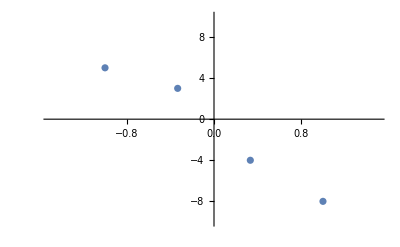

```mathematica
lp=ListPlot[{{-1,ym1},{-1/3,ym13},{1/3,y13},{1,y1}},PlotRange->{{-1.5,1.5},{-10,10}}]
```

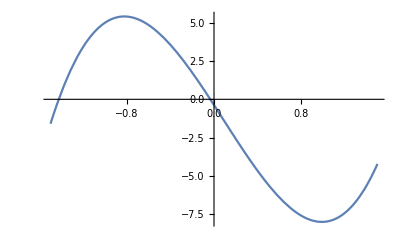

```mathematica
p=Plot[f[x],{x,-1.5,1.5}]
```

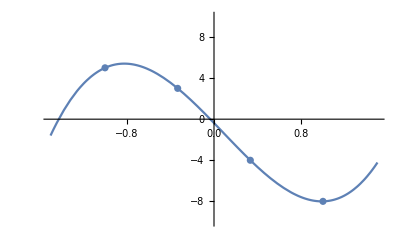

```mathematica
Show[lp,p]
```